```mathematica
RatioSubGood[tuple_, subTuple_, range_] := Module[
{vote, count, countGood, distances, div, result},
count=1;
vote = 0;
div=1;
countGood=0;
result={};
Monitor[
While[count ≤ range,
distances = ParallelTable[Distance[vote,p],{p,tuple}];
If[Max[ParallelTable[Distance[vote,p],{p,subTuple}]] ==0,
countGood = countGood+1;
];
If[Mod[count,div]==0,
result =Append[result,{div,countGood/(count)}];
Print[{div,countGood/(count)}];
div=div*Product[p,{p,subTuple}];
];
If [Max[distances] == 0,
(* found a good *)
vote++;
If[Min[ParallelTable[Distance[vote,p],{p,tuple}]]==0,
count+=1
],
vote += Max[distances];
count+=1;
];
],
{count, range,div}
];
Return[result];
]
```

```mathematica
RatioSubGood[{3,5},{5},5^10+1]
```

{1,1}

{5,5/7}

{25,5/7}

{125,125/179}

{625,625/934}

{3125,3125/4687}

{15625,15625/23402}

{78125,78125/116954}

{390625,390625/584646}

{1953125,390625/584926}

{{1,1},{5,5/7},{25,5/7},{125,125/179},{625,625/934},{3125,3125/4687},{15625,15625/23402},{78125,78125/116954},{390625,390625/584646},{1953125,390625/584926}}

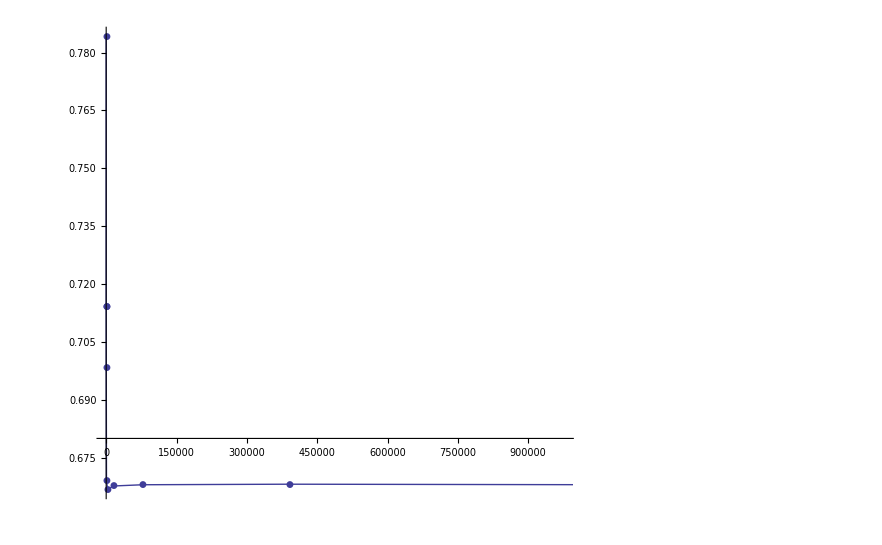

```mathematica
ListLinePlot[%,PlotMarkers->Automatic]
```

```mathematica
N[5^20]
```

9.53674×10^13

```mathematica
RatioSubGood[{3,5},{3},3^18+1]
```

{1,1}

{3,2/3}

{9,2/3}

{27,19/27}

{81,53/81}

{243,157/243}

{729,472/729}

{2187,1418/2187}

{6561,1421/2187}

{19683,4259/6561}

{59049,38266/59049}

{177147,114838/177147}

{531441,344579/531441}

{1594323,1033322/1594323}

{4782969,3099499/4782969}

{14348907,9300125/14348907}

$Aborted

```mathematica
v={{1,1}, {3,2/3}, {9,2/3}, {27,19/27},{81,53/81},{243,157/243},{729,472/729},{2187,1418/2187},{6561,1421/2187},{19683,4259/6561},{59049,38266/59049},{177147,114838/177147},{531441,344579/531441},{1594323,1033322/1594323},{4782969,3099499/4782969}, {14348907,9300125/14348907}}
```

{{1,1},{3,2/3},{9,2/3},{27,19/27},{81,53/81},{243,157/243},{729,472/729},{2187,1418/2187},{6561,1421/2187},{19683,4259/6561},{59049,38266/59049},{177147,114838/177147},{531441,344579/531441},{1594323,1033322/1594323},{4782969,3099499/4782969},{14348907,9300125/14348907}}

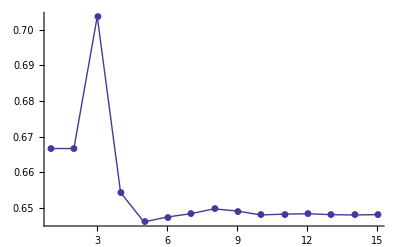

```mathematica
ListLinePlot[Take[Map[#[[2]]&,v],{2,16}],PlotMarkers->Automatic, PlotRange->All]
```

```mathematica
N[9/25]
```

0.36

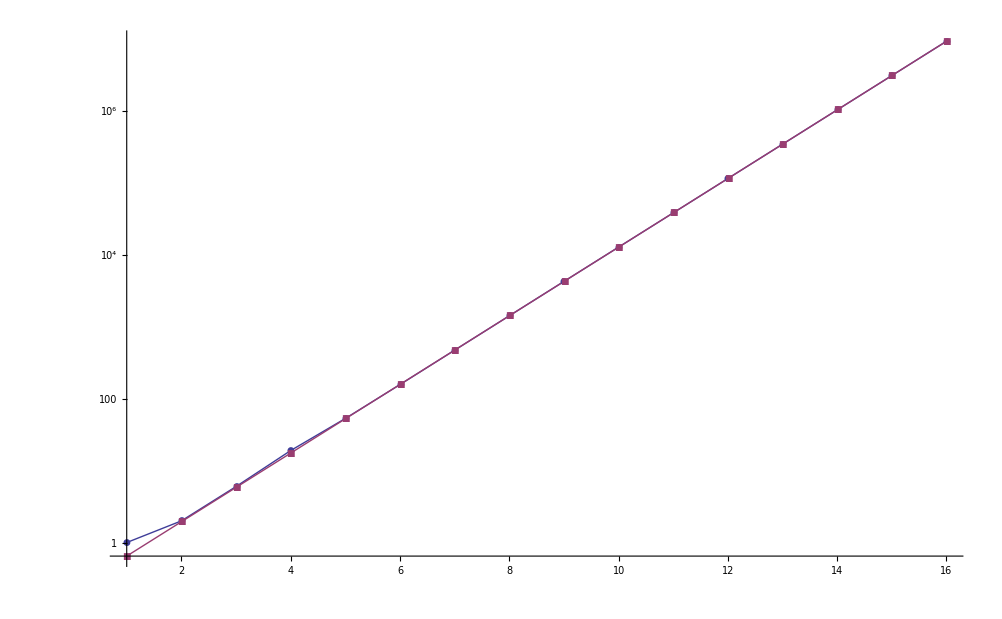

```mathematica
ListLogPlot[{w, With[{a=0.21604354579212182},Table[a  3^x,{x,1,16}]]},PlotMarkers->Automatic, PlotRange->All, Joined->True]
```

```mathematica
N[Log[3,1000000000]]
```

18.8631

```mathematica
N[Mean[Take[Map[#[[2]]&,Out[178]],{2,9}]]]
```

0.66038

```mathematica
w=Map[#[[1]]*#[[2]]&,v]
```

{1,2,6,19,53,157,472,1418,4263,12777,38266,114838,344579,1033322,3099499,9300125}

```mathematica
FindFit[w, a  3^x,{a,b},x]
```

{a→0.216044,b→0.}

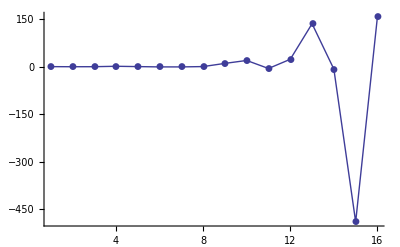

```mathematica
ListPlot[With[{a=0.21604354579212182},Table[w[[x]]-a  3^x,{x,1,16}]],PlotMarkers->Automatic, PlotRange->All, Joined->True]
```